## CellVertexNumbers-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Fri 9 Nov 2012 04:14:21
using xCellerator 0.90 and XSSA 1204002

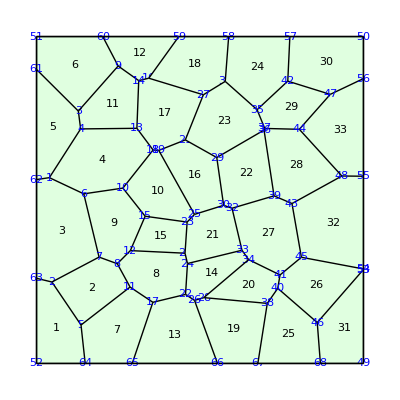

```mathematica
w=TemplateRandomSquareGrid[36, {-5,-5}, {5, 5}];
ShowTissue[w, "CellNumbers"-> True, "VertexNumbers"-> Directive[Blue, FontFamily-> "Verdana"]]
```

Determine the vertex numbers for cell 15

```mathematica
CellVertexNumbers[w,15]
```

{12,20,23,15}

Determine the edge numbers for cell 15

```mathematica
c15=TissueCells[w][[15]]
```

{24,36,28,23}

Determine the edge numbers for cell 23

```mathematica
c23=TissueCells[w][[23]]
```

{38,39,51,61,59,53,47}

Find the list of all edges

```mathematica
e=TissueEdges[w]
```

{{1,4},{1,6},{1,62},{2,5},{2,7},{2,63},{3,4},{3,9},{3,61},{4,13},{5,11},{5,64},{6,7},{6,10},{7,8},{8,11},{8,12},{9,14},{9,60},{10,15},{10,18},{11,17},{12,15},{12,20},{13,14},{13,18},{14,16},{15,23},{16,27},{16,59},{17,22},{17,65},{18,19},{19,21},{19,25},{20,23},{20,24},{21,27},{21,29},{22,24},{22,26},{23,25},{24,33},{25,30},{26,28},{26,66},{27,31},{28,34},{28,38},{29,30},{29,36},{30,32},{31,35},{31,58},{32,33},{32,39},{33,34},{34,41},{35,37},{35,42},{36,37},{36,39},{37,44},{38,40},{38,67},{39,43},{40,41},{40,46},{41,45},{42,47},{42,57},{43,45},{43,48},{44,47},{44,48},{45,54},{46,53},{46,68},{47,56},{48,55},{49,53},{49,68},{50,56},{50,57},{51,60},{51,61},{52,63},{52,64},{53,54},{54,55},{55,56},{57,58},{58,59},{59,60},{61,62},{62,63},{64,65},{65,66},{66,67},{67,68}}

Find the vertex numbers for cell 15

```mathematica
CellVertexNumbers[c15, e]
```

{12,20,23,15}

Find the vertex numbers for cells 15 and 23

```mathematica
CellVertexNumbers[{c15,c23}, e]
```

{{12,20,23,15},{21,27,31,35,37,36,29}}

Find the list of vertex numbers for every cell in the tissue

```mathematica
CellVertexNumbers[w]
```

{{52,64,5,2,63},{2,5,11,8,7},{62,63,2,7,6,1},{1,6,10,18,13,4},{61,62,1,4,3},{51,61,3,9,60},{64,65,17,11,5},{8,11,17,22,24,20,12},{6,7,8,12,15,10},{10,15,23,25,19,18},{3,4,13,14,9},{59,60,9,14,16},{65,66,26,22,17},{22,26,28,34,33,24},{12,20,23,15},{19,25,30,29,21},{13,14,16,27,21,19,18},{58,59,16,27,31},{66,67,38,28,26},{28,38,40,41,34},{23,25,30,32,33,24,20},{29,30,32,39,36},{21,27,31,35,37,36,29},{57,58,31,35,42},{67,68,46,40,38},{53,54,45,41,40,46},{32,33,34,41,45,43,39},{36,39,43,48,44,37},{35,37,44,47,42},{50,57,42,47,56},{46,53,49,68},{54,55,48,43,45},{55,56,47,44,48}}